# Spin interaction

```mathematica
Jz=1/2{{1,0},{0,-1}};
Jx=1/2{{0,1},{1,0}};
Jy=1/2{{0,-ⅈ},{ⅈ,0}};
II={{1,0},{0,1}};
```

```mathematica
(* direct Product space *)
```

```mathematica
I4=IdentityMatrix[4];
Sz=KroneckerProduct[Jz,II];
Sx=KroneckerProduct[Jx,II];
Sy=KroneckerProduct[Jy,II];
Sp=KroneckerProduct[Jx+ⅈ Jy,II];
Sm=KroneckerProduct[Jx-ⅈ Jy,II];
Iz=KroneckerProduct[II,Jz];
Ix=KroneckerProduct[II,Jx];
Iy=KroneckerProduct[II,Jy];
SzIz=KroneckerProduct[Jz,Jz];
SzIy=KroneckerProduct[Jz,Jy];
SxIx=KroneckerProduct[Jx,Jx];
SxIy=KroneckerProduct[Jx,Jy];
SyIy=KroneckerProduct[Jy,Jy];
SzIx=KroneckerProduct[Jz,Jx];
SzIy=KroneckerProduct[Jz,Jy];
SxIz=KroneckerProduct[Jx,Jz];
SpIm=KroneckerProduct[Jx+ⅈ Jy,Jx-ⅈ Jy];
SmIp=KroneckerProduct[Jx-ⅈ Jy,Jx+ⅈ Jy];
SpIp=KroneckerProduct[Jx+ⅈ Jy,Jx+ⅈ Jy];
SmIm=KroneckerProduct[Jx-ⅈ Jy,Jx-ⅈ Jy];
SzIp=KroneckerProduct[Jz,Jx+ⅈ Jy];
SzIm=KroneckerProduct[Jz,Jx-ⅈ Jy];
```

```mathematica
ρ0[Pe0_,PI0_]:=Pe0 Sz+PI0 Iz;
```

```mathematica
H[a1_,a2_,b1_,c_,d_,ω_,t_]:=a1 Sz +a2 Iz+ b1 (Sx Cos[ω t]+Sy Sin[ω t])+ c SzIz+d SzIx ;
H[a1,a2,b1,c,d,ω,t]//MatrixForm
HR[a1_,a2_,b1_,c_,d_,ω_,t_]:= MatrixExp[ⅈ Sz ω t ]. H[a1,a2,b1,c,d,ω,t]. MatrixExp[-ⅈ Sz ω t]-ω Sz//Simplify;
HR[a1,a2,b1,c,d,ω,t]//MatrixForm
```

(a1/2+a2/2+c/4 | d/4 | b1 (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω]) | 0
d/4 | a1/2-a2/2-c/4 | 0 | b1 (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω])
b1 (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | 0 | -a1/2+a2/2-c/4 | -d/4
0 | b1 (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | -d/4 | -a1/2-a2/2+c/4)

(1/4 (2 a1+2 a2+c-2 ω) | d/4 | b1/2 | 0
d/4 | 1/4 (2 a1-2 a2-c-2 ω) | 0 | b1/2
b1/2 | 0 | 1/4 (-2 a1+2 a2-c+2 ω) | -d/4
0 | b1/2 | -d/4 | 1/4 (-2 a1-2 a2+c+2 ω))

```mathematica
ρ[a1_,a2_,b1_,c_,d_,ω_,t_,Pe0_,PI0_]:=Module[
{G},
G=N[HR[a1,a2,b1,c,d,ω,t]];
MatrixExp[-ⅈ G t]. ρ0[Pe0,PI0].MatrixExp[ⅈ G t]
]
Pe[a1_,a2_,b1_,c_,d_,ω_,t_,Pe0_,PI0_]:=Module[{G},
G=N[HR[a1,a2,b1,c,d,ω,t]];
Re[2Tr[Sz.MatrixExp[-ⅈ G t]. ρ0[Pe0,PI0].MatrixExp[ⅈ G t]]]]
PI[a1_,a2_,b1_,c_,d_,ω_,t_,Pe0_,PI0_]:=Module[{G},
G=N[HR[a1,a2,b1,c,d,ω,t]];
Re[2Tr[Iz.MatrixExp[-ⅈ G t]. ρ0[Pe0,PI0].MatrixExp[ⅈ G t]]]]
```

```mathematica
Manipulate[
Plot[{
Pe[a1,a2,b1,c,3,ω,t,1,0],
PI[a1,a2,b1,c,3,ω,t,1,0]
}
,{t,0,10},PlotRange->All],{a1,1,2},{a2,1,2},{b1,1,2},{c,0,1},{ω,1,2}]
```

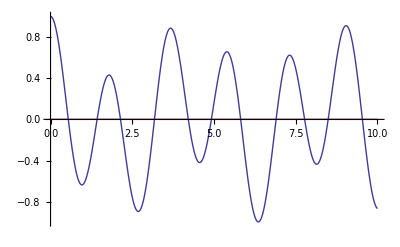

```mathematica
Plot[{
Pe[2.2,-1.7,3,0.25,3,2.2,t,1,0],
PI[2.2,-1.7,3,0.25,3,2.2,t,1,0]
}
,{t,0,10},PlotRange->All]
```

```mathematica
Manipulate[NumberForm[Chop[ρ[2.2,-1.7,-1.7,0.25,3,2.2,t,1,0]]//Simplify//MatrixForm,2],
{t,0,3}]
```

```mathematica
Manipulate[2 a KroneckerProduct[Jz,II]+2b KroneckerProduct[II,Jz]//MatrixForm,
{{a,0.25},0,1},{{b,0.25},0,1}]
```

```mathematica
Tr[Iz.(P Sz+Q Iz)]//MatrixForm
```

Q

```mathematica
2Tr[Sz.KroneckerProduct[P Jz,Q Jz]]//Simplify
```

0